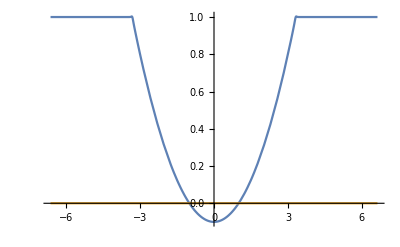

```mathematica
(*Configuration*)
a=0.1;
ν=0.0000001;

n=100; b=(1+1/a)^(-n);
V=Function[x,-(a*(x^2-1)+ⅈ*ν-1)/(1+b*x^(2n))];
Epsilon = Function[x,1-V[x]];

X0=2*Sqrt[1+1/a];
Plot[{Re[Epsilon[x]],Im[Epsilon[x]]},{x,-X0,X0},PlotRange->Full]

A=1;
```

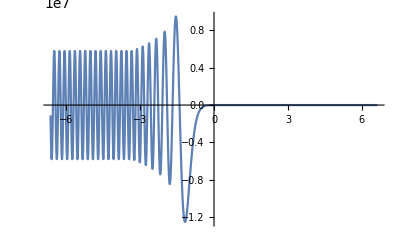

0.0000356109

```mathematica
(*TE-wave*)
values={χ->30,θ->0};
ETEEquation={y''[x]+χ^2*(Epsilon[x]-Sin[θ]^2)*y[x]==0};
ETEInitials={y[X0]==A,y'[X0]==ⅈ*χ*A} (* χ=k0*L, where L is a width of the layer *);

ETE=NDSolveValue[{ETEEquation,ETEInitials}/.values,y,{x,-X0,X0}];
Plot[Re[ETE[x]],{x,-X0,X0},PlotRange->Full]

RTE=Exp[2*ⅈ*χ*Cos[θ]*(-X0)]*(ⅈ*χ*Cos[θ]*ETE[-X0]-ETE'[-X0])/(ⅈ*χ*Cos[θ]*ETE[-X0]+ETE'[-X0]);
TTE=ETE[X0]*Exp[-ⅈ*χ*Cos[θ]*(X0)]*(Exp[ⅈ*χ*Cos[θ]*(-X0)]+RTE*Exp[-ⅈ*χ*Cos[θ]*(-X0)])/ETE[-X0];

TEDissipation =1 - Abs[RTE]^2-Abs[TTE]^2;
TEDissipation/.values
```

```mathematica
TEDissipationFromΘ={};
begining=-π/2;end=π/2;nstep=100;
ProgressIndicator[Dynamic[(Θ-begining)/(end-begining)]]
For[Θ=begining,Θ<end,Θ+=(end-begining)/nstep,
values={χ->30,θ->Θ};
ETE=NDSolveValue[{ETEEquation,ETEInitials}/.values,y,{x,-X0,X0}];
RTE=Exp[2*ⅈ*χ*Cos[θ]*(-X0)]*(ⅈ*χ*Cos[θ]*ETE[-X0]-ETE'[-X0])/(ⅈ*χ*Cos[θ]*ETE[-X0]+ETE'[-X0]);
TTE=ETE[X0]*Exp[-ⅈ*χ*Cos[θ]*(X0)]*(Exp[ⅈ*χ*Cos[θ]*(-X0)]+RTE*Exp[-ⅈ*χ*Cos[θ]*(-X0)])/ETE[-X0];
TEDissipation =1 - Abs[RTE]^2-Abs[TTE]^2;
TEDissipationFromΘ=Append[TEDissipationFromΘ,{Θ,TEDissipation/.values}];
];
```

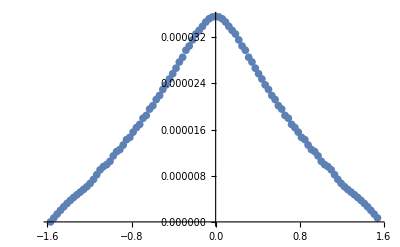

```mathematica
ListPlot[TEDissipationFromΘ]
```

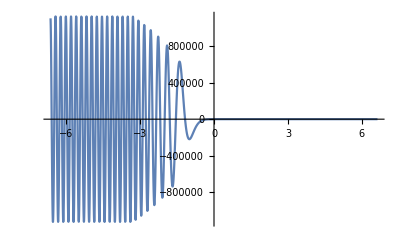

0.0000355842

```mathematica
(*TM-wave*)
values={χ->30,θ->0};
BTMEquation={y''[x]-(Epsilon'[x]/Epsilon[x])*y'[x]+χ^2*(Epsilon[x]-Sin[θ]^2)*y[x]==0};
BTMInitials={y[X0]==-A,y'[X0]==-ⅈ*χ*Epsilon[X0]*A*Cos[θ]};

BTM=NDSolveValue[{BTMEquation,BTMInitials}/.values,y,{x,-X0,X0}];
Plot[Re[BTM[x]],{x,-X0,X0},PlotRange->Full]

RTM=Exp[2*ⅈ*χ*Cos[θ]*(-X0)]*(ⅈ*χ*Cos[θ]*BTM[-X0]-BTM'[-X0])/(ⅈ*χ*Cos[θ]*BTM[-X0]+BTM'[-X0]);
TTM=BTM[X0]*Exp[-ⅈ*χ*Cos[θ]*(X0)]*(Exp[ⅈ*χ*Cos[θ]*(-X0)]+RTM*Exp[-ⅈ*χ*Cos[θ]*(-X0)])/BTM[-X0];

TMDissipation=1-Abs[RTM]^2-Abs[TTM]^2;
TMDissipation/.values
```

```mathematica
TMDissipationFromΘ={};
begining=-0.3;end=0.3;nstep=100;
ProgressIndicator[Dynamic[(Θ-begining)/(end-begining)]]
For[Θ=begining,Θ<end,Θ+=(end-begining)/nstep,
values={χ->250,θ->Θ};
BTM=NDSolveValue[{BTMEquation,BTMInitials}/.values,y,{x,-X0,X0}];
RTM=Exp[2*ⅈ*χ*Cos[θ]*(-X0)]*(ⅈ*χ*Cos[θ]*BTM[-X0]-BTM'[-X0])/(ⅈ*χ*Cos[θ]*BTM[-X0]+BTM'[-X0]);
TTM=BTM[X0]*Exp[-ⅈ*χ*Cos[θ]*(X0)]*(Exp[ⅈ*χ*Cos[θ]*(-X0)]+RTM*Exp[-ⅈ*χ*Cos[θ]*(-X0)])/BTM[-X0];
TMDissipation=1-Abs[RTM]^2-Abs[TTM]^2;
TMDissipationFromΘ=Append[TMDissipationFromΘ,{Θ,TMDissipation/.values}];
];
```

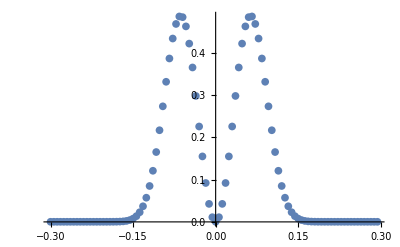

```mathematica
ListPlot[TMDissipationFromΘ]
```

```mathematica
TMDissipationFromΧ={};
begining=10;end=250;nstep=250;
ProgressIndicator[Dynamic[(Χ-begining)/(end-begining)]]
For[Χ=begining,Χ<end,Χ+=(end-begining)/nstep,
values={χ->Χ,θ->0.424015*Χ^(-0.347467)};
BTM=NDSolveValue[{BTMEquation,BTMInitials}/.values,y,{x,-X0,X0}];
RTM=Exp[2*ⅈ*χ*Cos[θ]*(-X0)]*(ⅈ*χ*Cos[θ]*BTM[-X0]-BTM'[-X0])/(ⅈ*χ*Cos[θ]*BTM[-X0]+BTM'[-X0]);
TTM=BTM[X0]*Exp[-ⅈ*χ*Cos[θ]*(X0)]*(Exp[ⅈ*χ*Cos[θ]*(-X0)]+RTM*Exp[-ⅈ*χ*Cos[θ]*(-X0)])/BTM[-X0];
TMDissipation=1-Abs[RTM]^2-Abs[TTM]^2;
TMDissipationFromΧ=Append[TMDissipationFromΧ,{Χ,TMDissipation/.values}];
];
```

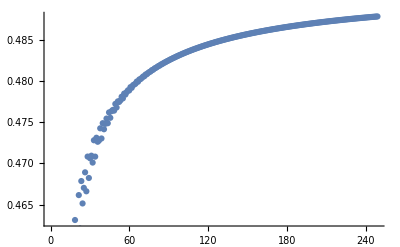

```mathematica
ListPlot[TMDissipationFromΧ]
```

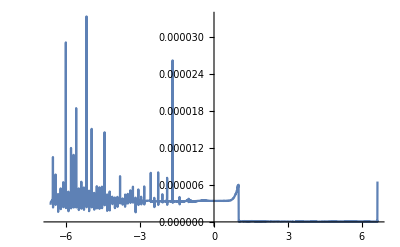

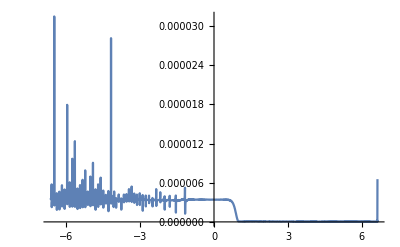

```mathematica
(*Reletive precision*)
values={θ->0,χ->30};

ETE=NDSolveValue[{ETEEquation,ETEInitials}/.values,y,{x,-X0,X0}];
BTM=NDSolveValue[{BTMEquation,BTMInitials}/.values,y,{x,-X0,X0}];
ETM=Function[x,ⅈ*BTM'[x]/(χ*Epsilon[x])];
BTE=Function[x,(-ⅈ/χ)*ETE'[x]];

Plot[Abs[ETE[x]-ETM[x]]/Min[Abs[ETE[x]],Abs[ETM[x]]]/.values,{x,-X0,X0},PlotRange->Full]
Plot[Abs[BTE[x]+BTM[x]]/Min[Abs[BTE[x]],Abs[BTM[x]]]/.values,{x,-X0,X0},PlotRange->Full]
```

```mathematica
(*Anisotropy*)
T={{ⅈ,-ⅈ,0},{1,1,0},{0,0,1}} (*Matrix to diagonalize permittivity*);
P[x_]=T.{{1-V[x]/(1+υ),0,0},{0,1-V[x]/(1-υ),0},{0,0,1-V[x]}}.Inverse[T] (*Permittivity, from diagonal to usual*);

GeneralSystem = {
(*Ex[x]*P[x][[1,1]]+Ey[x]*P[x][[1,2]]==kz*By[x]-ky*Bz[x],
Bx[x]==ky*Ez[x]-kz*Ey[x],*)
Ey'[x]==ⅈ*χ*(ky*(kz*By[x]-ky*Bz[x]-Ey[x]*P[x][[1,2]])/P[x][[1,1]]+Bz[x]),(*Ey'[x]==ⅈ*χ*(ky*Ex[x]+Bz[x])*)
Ez'[x]==ⅈ*χ*(kz*(kz*By[x]-ky*Bz[x]-Ey[x]*P[x][[1,2]])/P[x][[1,1]]-By[x]),(*Ez'[x]==ⅈ*χ*(kz*Ex[x]-By[x])*)
By'[x]==ⅈ*χ*(ky*(ky*Ez[x]-kz*Ey[x])-P[x][[3,3]]*Ez[x]),(*By'[x]==ⅈ*χ*(ky*Bx[x]-P[x][[3,3]]*Ez[x])*)
Bz'[x]==ⅈ*χ*(kz*(ky*Ez[x]-kz*Ey[x])+P[x][[2,1]]*(kz*By[x]-ky*Bz[x]-Ey[x]*P[x][[1,2]])/P[x][[1,1]]+P[x][[2,2]]*Ey[x])
(*Bz'[x]==ⅈ*χ*(kz*Bx[x]+P[x][[2,1]]*Ex[x]+P[x][[2,2]]*Ey[x])*)
}/.{kx->Cos[ϕ]Cos[θ],ky->Cos[ϕ]Sin[θ],kz->Sin[ϕ]};

GeneralInitials = { 
(*Ex[X0]==A*(Sin[θ]Sin[α]-Cos[ϕ]Cos[θ]Cos[α]),*)
Ey[X0]==-A*(Sin[θ]Sin[ϕ]Cos[α]+Cos[θ]Sin[α]),
Ez[X0]==A*Cos[ϕ]Cos[α],
(*Bx[X0]==A*(Sin[θ]Cos[α]+Cos[ϕ]Cos[θ]Sin[α]),*)
By[X0]==A*(Sin[θ]Sin[ϕ]Sin[α]-Cos[θ]Cos[α]),
Bz[X0]==-A*Cos[ϕ]Sin[α]
};

values={χ->30,θ->0,ϕ->0,α->0,υ->10^(-3)} (* υ = |eB/(mcw)|, so for B~1000G U~10^(-10) *);
Solution = NDSolveValue[{GeneralSystem,GeneralInitials}/.values,{Ey,Ez,By,Bz},{x,-X0,X0}];

Eτ=Function[x,If[Solution[[1]][X0]==0,Solution[[2]][x],Solution[[1]][x]]];
Plot[Re[Eτ[x]],{x,-X0,X0}]

R=Exp[2*ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)]*(ⅈ*χ*Cos[ϕ]Cos[θ]*Eτ[-X0]-Eτ'[-X0])/(ⅈ*χ*Cos[ϕ]Cos[θ]*Eτ[-X0]+Eτ'[-X0]);
T=Eτ[X0]*Exp[-ⅈ*χ*Cos[ϕ]Cos[θ]*(X0)]*(Exp[ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)]+R*Exp[-ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)])/Eτ[-X0];
Dissipation = 1 - Abs[R]^2-Abs[T]^2;
Dissipation/.values
```

-Graphics-

0.0000356109

```mathematica
DissipationFromΑ={};
begining=-π; end=π; nstep=100;
ProgressIndicator[Dynamic[(Α-begining)/(end-begining)]]
For[Α=begining,Α<end,Α+=(end-begining)/nstep,
values={χ->30,θ->0,ϕ->0,α->Α,υ->10^(-3)};
Solution = NDSolveValue[{GeneralSystem,GeneralInitials}/.values,{Ey,Ez,By,Bz},{x,-X0,X0},AccuracyGoal->10];
Eτ=Function[x,If[Solution[[1]][X0]==0,Solution[[2]][x],Solution[[1]][x]]];
R=Exp[2*ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)]*(ⅈ*χ*Cos[ϕ]Cos[θ]*Eτ[-X0]-Eτ'[-X0])/(ⅈ*χ*Cos[ϕ]Cos[θ]*Eτ[-X0]+Eτ'[-X0]);
T=Eτ[X0]*Exp[-ⅈ*χ*Cos[ϕ]Cos[θ]*(X0)]*(Exp[ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)]+R*Exp[-ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)])/Eτ[-X0];
Dissipation = 1 - Abs[R]^2-Abs[T]^2;
DissipationFromΑ=Append[DissipationFromΑ,{Α,Dissipation/.values}];
];
```

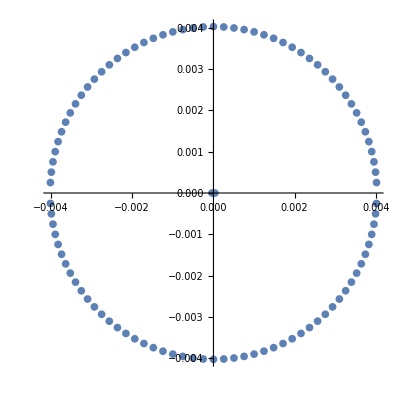

```mathematica
ListPolarPlot[DissipationFromΑ]
```

```mathematica
DissipationFromΘ={};
begining=-0.3; end=0.3; nstep=100;
ProgressIndicator[Dynamic[(Θ-begining)/(end-begining)]]
For[Θ=begining,Θ<end,Θ+=(end-begining)/nstep,
values={χ->250,θ->Θ,ϕ->0,α->π/2,υ->10^(-3)};
Solution = NDSolveValue[{GeneralSystem,GeneralInitials}/.values,{Ey,Ez,By,Bz},{x,-X0,X0}];
Eτ=Function[x,If[Solution[[1]][X0]==0,Solution[[2]][x],Solution[[1]][x]]];
R=Exp[2*ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)]*(ⅈ*χ*Cos[ϕ]Cos[θ]*Eτ[-X0]-Eτ'[-X0])/(ⅈ*χ*Cos[ϕ]Cos[θ]*Eτ[-X0]+Eτ'[-X0]);
T=Eτ[X0]*Exp[-ⅈ*χ*Cos[ϕ]Cos[θ]*(X0)]*(Exp[ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)]+R*Exp[-ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)])/Eτ[-X0];
Dissipation = 1 - Abs[R]^2-Abs[T]^2;
DissipationFromΘ=Append[DissipationFromΘ,{Θ,Dissipation/.values}];
];
```

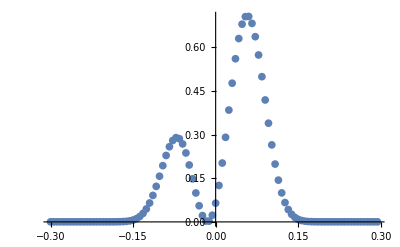

```mathematica
ListPlot[DissipationFromΘ]
```

```mathematica
TMDissipationFromΧ={};
begining=10;end=250;nstep=250;
ProgressIndicator[Dynamic[(Χ-begining)/(end-begining)]]
For[Χ=begining,Χ<end,Χ+=(end-begining)/nstep,
values={χ->Χ,θ->0.424015*Χ^(-0.347467),ϕ->0,α->π/2,υ->10^(-3)};
Solution = NDSolveValue[{GeneralSystem,GeneralInitials}/.values,{Ey,Ez,By,Bz},{x,-X0,X0}];
Eτ=Function[x,If[Solution[[1]][X0]==0,Solution[[2]][x],Solution[[1]][x]]];
R=Exp[2*ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)]*(ⅈ*χ*Cos[ϕ]Cos[θ]*Eτ[-X0]-Eτ'[-X0])/(ⅈ*χ*Cos[ϕ]Cos[θ]*Eτ[-X0]+Eτ'[-X0]);
T=Eτ[X0]*Exp[-ⅈ*χ*Cos[ϕ]Cos[θ]*(X0)]*(Exp[ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)]+R*Exp[-ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)])/Eτ[-X0];
Dissipation = 1 - Abs[R]^2-Abs[T]^2;
TMDissipationFromΧ=Append[TMDissipationFromΧ,{Χ,Dissipation/.values}];
];
```

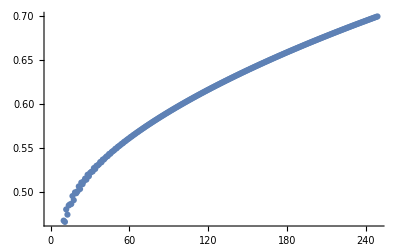

```mathematica
ListPlot[TMDissipationFromΧ]
```

```mathematica
RandomDissipation3D={};
npoint=1000;
ProgressIndicator[Dynamic[i/npoint]]
For[i=0,i<npoint,i++,
values={χ->30,θ->RandomReal[{-π/2,π/2}],ϕ->RandomReal[{-π/2,π/2}],α->RandomReal[{-π,π}],υ->10^(-3)};
Solution = NDSolveValue[{GeneralSystem,GeneralInitials}/.values,{Ey,Ez,By,Bz},{x,-X0,X0},AccuracyGoal->10];
Eτ=Function[x,If[Solution[[1]][X0]==0,Solution[[2]][x],Solution[[1]][x]/Cos[ArcTan[Abs[Solution[[2]][X0]]/Abs[Solution[[1]][X0]]]]]];
R=Exp[2*ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)]*(ⅈ*χ*Cos[ϕ]Cos[θ]*Eτ[-X0]-Eτ'[-X0])/(ⅈ*χ*Cos[ϕ]Cos[θ]*Eτ[-X0]+Eτ'[-X0]);
T=Eτ[X0]*Exp[-ⅈ*χ*Cos[ϕ]Cos[θ]*(X0)]*(Exp[ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)]+R*Exp[-ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)])/Eτ[-X0];
Dissipation = 1 - Abs[R]^2-Abs[T]^2;
RandomDissipation3D=Append[RandomDissipation3D,{ϕ,α,θ,Dissipation}/.values];
];
ListContourPlot3D[ RandomDissipation3D,PlotLegends->"Expressions",AxesLabel->{ϕ,α,θ}]
```

-Graphics3D-

```mathematica
RandomDissipation={};
npoint=1000;
ProgressIndicator[Dynamic[i/npoint]]
For[i=0,i<npoint,i++,
values={χ->30,θ->RandomReal[{-π/2,π/2}],ϕ->RandomReal[{-π/2,π/2}],α->1,υ->10^(-3)};
Solution = NDSolveValue[{GeneralSystem,GeneralInitials}/.values,{Ey,Ez,By,Bz},{x,-X0,X0}];
Eτ=Function[x,If[Solution[[1]][X0]==0,Solution[[2]][x],Solution[[1]][x]/Cos[ArcTan[Abs[Solution[[2]][X0]]/Abs[Solution[[1]][X0]]]]]];

Eτ=Function[x,Solution[[1]][x]];
R=Exp[2*ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)]*(ⅈ*χ*Cos[ϕ]Cos[θ]*Eτ[-X0]-Eτ'[-X0])/(ⅈ*χ*Cos[ϕ]Cos[θ]*Eτ[-X0]+Eτ'[-X0]);
T=Eτ[X0]*Exp[-ⅈ*χ*Cos[ϕ]Cos[θ]*(X0)]*(Exp[ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)]+R*Exp[-ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)])/Eτ[-X0];
Dissipation = (1 - Abs[R]^2-Abs[T]^2)*Abs[Sin[θ]Sin[ϕ]Cos[α]+Cos[θ]Sin[α]]/.values;

Eτ=Function[x,Solution[[2]][x]];
R=Exp[2*ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)]*(ⅈ*χ*Cos[ϕ]Cos[θ]*Eτ[-X0]-Eτ'[-X0])/(ⅈ*χ*Cos[ϕ]Cos[θ]*Eτ[-X0]+Eτ'[-X0]);
T=Eτ[X0]*Exp[-ⅈ*χ*Cos[ϕ]Cos[θ]*(X0)]*(Exp[ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)]+R*Exp[-ⅈ*χ*Cos[ϕ]Cos[θ]*(-X0)])/Eτ[-X0];
Dissipation += (1 - Abs[R]^2-Abs[T]^2)*Abs[Cos[ϕ]Cos[α]]/.values;

RandomDissipation=Append[RandomDissipation,{ϕ,θ,Dissipation}/.values];
];
ListPointPlot3D[ RandomDissipation,PlotLegends->"Expressions",AxesLabel->{ϕ,θ,Δ},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

-Graphics-

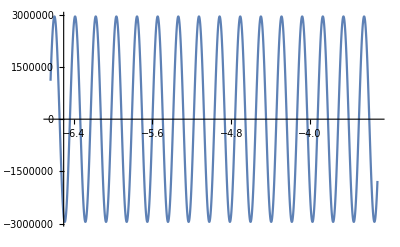

```mathematica
values={χ->30,θ->0,ϕ->0,α->0,υ->10^(-3)} (* υ = |eB/(mcw)|, so for B~1000G U~10^(-10) *);
Solution = NDSolveValue[{GeneralSystem,GeneralInitials}/.values,{Ey,Ez,By,Bz},{x,-X0,X0}];

Eτ=Function[x,If[Solution[[1]][X0]==0,Solution[[2]][x],Solution[[1]][x]]];
Plot[Re[Eτ[x]],{x,-X0,X0}]

Y1=Function[x,(Solution[[1]][x]+Solution[[4]][x])/2];
Y2=Function[x,(Solution[[1]][x]-Solution[[4]][x])/2];
Y3=Function[x,(Solution[[3]][x]+Solution[[2]][x])/2];
Y4=Function[x,(Solution[[3]][x]-Solution[[2]][x])/2];
Plot[Re[Y4[x]],{x,-X0,-X0/2}]
```

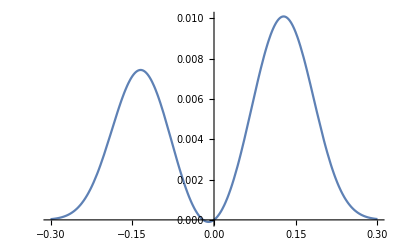

```mathematica
Plot[(Sin[x]^2+α*Sin[2x])Exp[-β*Abs[Sin[x]^3]]/.{α->0.01,β->300},{x,-0.3,0.3}]
```